```mathematica
vMatrix[n_Integer?Positive]:=Outer[Power,Table[Subscript[λ,i],{i,0,n-1}],Range[0,n-1]]
λs[n_]:=Table[Subscript[λ, i],{i,0,n-1}]
Z[d_,k_]:=Gamma[k*d]/Product[Gamma[d+1-j]*Gamma[k-j],{j,0,d-1}];
rule[d_]:=Subscript[λ, d-1]->1-Total@λs[d-1];
f[d_,k_]:=Product[Subscript[λ, i]^(k-d),{i,0,d-1}] Det[vMatrix[d]]^2/.rule[d];
```

```mathematica
pData={"c_0*l_0+c_0*l_1",
"c_0*l_0^2+c_0*l_0*l_1+c_1*l_0*l_1+c_0*l_1^2","c_0*l_0^3 + c_0*l_0^2*l_1 + 2*c_1*l_0^2*l_1 + c_0*l_0*l_1^2 + 2*c_1*l_0*l_1^2 + c_0*l_1^3","c_0*l_0^4+c_0*l_0^3*l_1+3*c_1*l_0^3*l_1+c_0*l_0^2*l_1^2+3*c_1*l_0^2*l_1^2+2*c_2*l_0^2*l_1^2+c_0*l_0*l_1^3+3*c_1*l_0*l_1^3+c_0*l_1^4","c_0*l_0^5 + c_0*l_0^4*l_1 + 4*c_1*l_0^4*l_1 + c_0*l_0^3*l_1^2 + 4*c_1*l_0^3*l_1^2 + 5*c_2*l_0^3*l_1^2 + c_0*l_0^2*l_1^3 + 4*c_1*l_0^2*l_1^3 + 5*c_2*l_0^2*l_1^3 + c_0*l_0*l_1^4 + 4*c_1*l_0*l_1^4 + c_0*l_1^5","c_0*l_0^6 + c_0*l_0^5*l_1 + 5*c_1*l_0^5*l_1 + c_0*l_0^4*l_1^2 + 5*c_1*l_0^4*l_1^2 + 9*c_2*l_0^4*l_1^2 + c_0*l_0^3*l_1^3 + 5*c_1*l_0^3*l_1^3 + 9*c_2*l_0^3*l_1^3 + 5*c_3*l_0^3*l_1^3 + c_0*l_0^2*l_1^4 + 5*c_1*l_0^2*l_1^4 + 9*c_2*l_0^2*l_1^4 + c_0*l_0*l_1^5 + 5*c_1*l_0*l_1^5 + c_0*l_1^6",
"c_0*l_0^7+c_0*l_0^6*l_1+6*c_1*l_0^6*l_1+c_0*l_0^5*l_1^2+6*c_1*l_0^5*l_1^2+14*c_2*l_0^5*l_1^2+c_0*l_0^4*l_1^3+6*c_1*l_0^4*l_1^3+14*c_2*l_0^4*l_1^3+14*c_3*l_0^4*l_1^3+c_0*l_0^3*l_1^4+6*c_1*l_0^3*l_1^4+14*c_2*l_0^3*l_1^4+14*c_3*l_0^3*l_1^4+c_0*l_0^2*l_1^5+6*c_1*l_0^2*l_1^5+14*c_2*l_0^2*l_1^5+c_0*l_0*l_1^6+6*c_1*l_0*l_1^6+c_0*l_1^7",
"c_0*l_0^8 + c_0*l_0^7*l_1 + 7*c_1*l_0^7*l_1 + c_0*l_0^6*l_1^2 + 7*c_1*l_0^6*l_1^2 + 20*c_2*l_0^6*l_1^2 + c_0*l_0^5*l_1^3 + 7*c_1*l_0^5*l_1^3 + 20*c_2*l_0^5*l_1^3 + 28*c_3*l_0^5*l_1^3 + c_0*l_0^4*l_1^4 + 7*c_1*l_0^4*l_1^4 + 20*c_2*l_0^4*l_1^4 + 28*c_3*l_0^4*l_1^4 + 14*c_4*l_0^4*l_1^4 + c_0*l_0^3*l_1^5 + 7*c_1*l_0^3*l_1^5 + 20*c_2*l_0^3*l_1^5 + 28*c_3*l_0^3*l_1^5 + c_0*l_0^2*l_1^6 + 7*c_1*l_0^2*l_1^6 + 20*c_2*l_0^2*l_1^6 + c_0*l_0*l_1^7 + 7*c_1*l_0*l_1^7 + c_0*l_1^8"};
optVars[p_]:=DeleteCases[Variables[ToExpression[pData[[p]],TeXForm]],Subscript[l, _]]
conds=Table[(0<=#<=1)&/@optVars[p],{p,1,8}];
trace[p_,d_]:=ToExpression[pData[[p]],TeXForm]//.{l->λ,rule[d]};
```

```mathematica
ToExpression[pData[[4]],TeXForm]/.l->λ //Simplify
```

c_0 (λ_0^4+λ_0^3 λ_1+λ_0^2 λ_1^2+λ_0 λ_1^3+λ_1^4)+λ_0 λ_1 (2 c_2 λ_0 λ_1+3 c_1 (λ_0^2+λ_0 λ_1+λ_1^2))

```mathematica
term0[d_,k_]:=Z[d,k]*Integrate[Boole[Max[λs[d]/.rule[d]]>=c]*f[d,k],λs[d-1]∈Simplex[d-1],Assumptions->{k∈,1/d<c<1}]
term1[p_,d_,k_]:=Z[d,k]*Integrate[trace[p,d]*Boole[Max[λs[d]/.rule[d]]<=c]*f[d,k],λs[d-1]∈Simplex[d-1],Assumptions->{k∈,1/d<c<1}]
term2[p_,d_,k_]:=Z[d,k]*Integrate[trace[p,d]*Boole[Max[λs[d]/.rule[d]]>=c]*f[d,k],λs[d-1]∈Simplex[d-1],Assumptions->{k∈,1/d<c<1}]
prob[p_,d_,k_]:=term0[d,k]+term1[p,d,k]-term2[p,d,k]
```

```mathematica
d=2;
pMax=8;
k=2;
probs=Table[prob[p,d,k],{p,1,pMax}];
maxprobs=Table[Maximize[{probs[[p]],conds[[p]],1/d<c<1},optVars[p]],{p,1,pMax}];
```

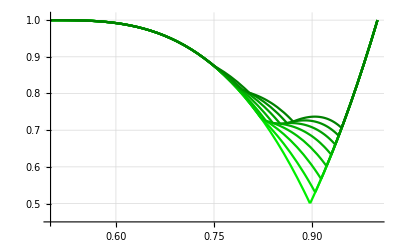

```mathematica
maxprobs[[All,1]];
Plot[%,{c,1/d,1},
PlotRange->{0.45,1.01},
GridLines->Automatic,
PlotStyle->Table[Darker[Green,p/2/pMax],{p,1,pMax}]]
```

```mathematica
maxprobs[[All,1]]//Simplify
```

{Piecewise[{{2-6 c+12 c^2-8 c^3, 4 c≤2+2^(2/3)}, {(-1+2 c)^3, True}}],Piecewise[{{2-6 c+12 c^2-8 c^3, Root-0.172Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,1]-0.17160487567952898≤c≤Root0.822Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,2]0.821569391081677}, {(-1+2 c)^3, Root0.905Root[-9+40 #1-100 #1^2+120 #1^3-80 #1^4+32 #1^5&,1]0.9047545552920163<c≤Root1.11Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,3]1.1086636977777937}, {17/10-6 c+18 c^2-28 c^3+24 c^4-(48 c^5)/5, Root0.822Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,2]0.821569391081677<c≤Root0.905Root[-9+40 #1-100 #1^2+120 #1^3-80 #1^4+32 #1^5&,1]0.9047545552920163||c<Root-0.172Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,1]-0.17160487567952898}, {-7/10+6 c-18 c^2+28 c^3-24 c^4+(48 c^5)/5, True}}],Piecewise[{{2-6 c+12 c^2-8 c^3, Root-0.172Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,1]-0.17160487567952898≤c≤Root0.822Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,2]0.821569391081677}, {(-1+2 c)^3, Root0.914Root[-3+15 #1-45 #1^2+70 #1^3-60 #1^4+24 #1^5&,1]0.9138308460911784<c≤Root1.11Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,3]1.1086636977777937}, {7/5-6 c+24 c^2-48 c^3+48 c^4-(96 c^5)/5, Root0.822Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,2]0.821569391081677<c≤Root0.914Root[-3+15 #1-45 #1^2+70 #1^3-60 #1^4+24 #1^5&,1]0.9138308460911784||c<Root-0.172Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,1]-0.17160487567952898}, {-2/5+6 c-24 c^2+48 c^3-48 c^4+(96 c^5)/5, True}}],Piecewise[{{2-6 c+12 c^2-8 c^3, Root-0.154Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,1]-0.15393049958952526≤c≤Root0.777Root[-3+280 #1^3-1260 #1^4+2184 #1^5-1680 #1^6+480 #1^7&,1]0.777014104230814}, {(-1+2 c)^3, Root0.922Root[-15+84 #1-294 #1^2+560 #1^3-630 #1^4+420 #1^5-168 #1^6+48 #1^7&,1]0.9221461872647261<c≤Root1.10Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,3]1.098601880564554}, {43/35-6 c+30 c^2-80 c^3+126 c^4-(612 c^5)/5+72 c^6-(144 c^7)/7, c<Root-0.154Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,1]-0.15393049958952526}, {8/7-6 c+30 c^2-72 c^3+90 c^4-60 c^5+24 c^6-(48 c^7)/7, Root0.829Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,2]0.8293850290372817<c≤Root0.922Root[-15+84 #1-294 #1^2+560 #1^3-630 #1^4+420 #1^5-168 #1^6+48 #1^7&,1]0.9221461872647261}, {-8/35+6 c-30 c^2+80 c^3-126 c^4+(612 c^5)/5-72 c^6+(144 c^7)/7, c>Root1.10Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,3]1.098601880564554}, {67/35-6 c+12 c^2-36 c^4+(312 c^5)/5-48 c^6+(96 c^7)/7, True}}],Piecewise[{{2-6 c+12 c^2-8 c^3, Root-0.138Root[3-84 #1^2+392 #1^3-840 #1^4+1008 #1^5-672 #1^6+192 #1^7&,1]-0.13818012415953612≤c≤Root0.777Root[-3+280 #1^3-1260 #1^4+2184 #1^5-1680 #1^6+480 #1^7&,1]0.777014104230814}, {(-1+2 c)^3, Root0.929Root[-9+56 #1-224 #1^2+504 #1^3-700 #1^4+616 #1^5-336 #1^6+96 #1^7&,1]0.9293389370049261<c≤Root1.09Root[3-84 #1^2+392 #1^3-840 #1^4+1008 #1^5-672 #1^6+192 #1^7&,3]1.0889856692514701}, {13/14-6 c+36 c^2-100 c^3+150 c^4-132 c^5+72 c^6-(144 c^7)/7, Root0.840Root[3-84 #1^2+392 #1^3-840 #1^4+1008 #1^5-672 #1^6+192 #1^7&,2]0.8400435950808649<c≤Root0.929Root[-9+56 #1-224 #1^2+504 #1^3-700 #1^4+616 #1^5-336 #1^6+96 #1^7&,1]0.9293389370049261}, {8/7-6 c+36 c^2-120 c^3+240 c^4-288 c^5+192 c^6-(384 c^7)/7, c<Root-0.138Root[3-84 #1^2+392 #1^3-840 #1^4+1008 #1^5-672 #1^6+192 #1^7&,1]-0.13818012415953612}, {-1/7+6 c-36 c^2+120 c^3-240 c^4+288 c^5-192 c^6+(384 c^7)/7, c>Root1.09Root[3-84 #1^2+392 #1^3-840 #1^4+1008 #1^5-672 #1^6+192 #1^7&,3]1.0889856692514701}, {25/14-6 c+12 c^2+12 c^3-90 c^4+156 c^5-120 c^6+(240 c^7)/7, True}}],Piecewise[{{2-6 c+12 c^2-8 c^3, Root-0.125Root[15-504 #1^2+2688 #1^3-6804 #1^4+10080 #1^5-9240 #1^6+5328 #1^7-2016 #1^8+448 #1^9&,1]-0.12458638284802992≤c≤Root0.747Root[3-1260 #1^4+7056 #1^5-15960 #1^6+18000 #1^7-10080 #1^8+2240 #1^9&,2]0.7469131623900309}, {(-1+2 c)^3, Root0.935Root[-21+144 #1-648 #1^2+1680 #1^3-2772 #1^4+3024 #1^5-2184 #1^6+1008 #1^7-288 #1^8+64 #1^9&,1]0.9354772246821378<c≤Root1.08Root[15-504 #1^2+2688 #1^3-6804 #1^4+10080 #1^5-9240 #1^6+5328 #1^7-2016 #1^8+448 #1^9&,3]1.0805619764567638}, {31/28-6 c+42 c^2-168 c^3+405 c^4-600 c^5+550 c^6-(2220 c^7)/7+120 c^8-(80 c^9)/3, Root-0.176Root[3-1260 #1^4+7056 #1^5-15960 #1^6+18000 #1^7-10080 #1^8+2240 #1^9&,1]-0.17625968513867118<c<Root-0.125Root[15-504 #1^2+2688 #1^3-6804 #1^4+10080 #1^5-9240 #1^6+5328 #1^7-2016 #1^8+448 #1^9&,1]-0.12458638284802992}, {15/14-6 c+42 c^2-168 c^3+420 c^4-684 c^5+740 c^6-(3720 c^7)/7+240 c^8-(160 c^9)/3, c≤Root-0.176Root[3-1260 #1^4+7056 #1^5-15960 #1^6+18000 #1^7-10080 #1^8+2240 #1^9&,1]-0.17625968513867118}, {55/28-6 c+12 c^2-8 c^3+15 c^4-84 c^5+190 c^6-(1500 c^7)/7+120 c^8-(80 c^9)/3, Root0.747Root[3-1260 #1^4+7056 #1^5-15960 #1^6+18000 #1^7-10080 #1^8+2240 #1^9&,2]0.7469131623900309<c≤Root0.783Root[-3+336 #1^3-1764 #1^4+4032 #1^5-5208 #1^6+4176 #1^7-2016 #1^8+448 #1^9&,1]0.7834367689893452}, {3/4-6 c+42 c^2-132 c^3+231 c^4-252 c^5+182 c^6-84 c^7+24 c^8-(16 c^9)/3, Root0.851Root[15-504 #1^2+2688 #1^3-6804 #1^4+10080 #1^5-9240 #1^6+5328 #1^7-2016 #1^8+448 #1^9&,2]0.8510935217615189<c≤Root0.935Root[-21+144 #1-648 #1^2+1680 #1^3-2772 #1^4+3024 #1^5-2184 #1^6+1008 #1^7-288 #1^8+64 #1^9&,1]0.9354772246821378}, {23/14-6 c+12 c^2+28 c^3-174 c^4+348 c^5-368 c^6+(1632 c^7)/7-96 c^8+(64 c^9)/3, Root0.783Root[-3+336 #1^3-1764 #1^4+4032 #1^5-5208 #1^6+4176 #1^7-2016 #1^8+448 #1^9&,1]0.7834367689893452<c≤Root0.851Root[15-504 #1^2+2688 #1^3-6804 #1^4+10080 #1^5-9240 #1^6+5328 #1^7-2016 #1^8+448 #1^9&,2]0.8510935217615189}, {-1/14+6 c-42 c^2+168 c^3-420 c^4+684 c^5-740 c^6+(3720 c^7)/7-240 c^8+(160 c^9)/3, c>Root1.14Root[3-1260 #1^4+7056 #1^5-15960 #1^6+18000 #1^7-10080 #1^8+2240 #1^9&,3]1.1398743779680676}, {-3/28+6 c-42 c^2+168 c^3-405 c^4+600 c^5-550 c^6+(2220 c^7)/7-120 c^8+(80 c^9)/3, True}}],Piecewise[{{2-6 c+12 c^2-8 c^3, Root-0.113Root[3-120 #1^2+720 #1^3-2100 #1^4+3696 #1^5-4200 #1^6+3120 #1^7-1440 #1^8+320 #1^9&,1]-0.11312525879060532≤c≤Root0.747Root[3-1260 #1^4+7056 #1^5-15960 #1^6+18000 #1^7-10080 #1^8+2240 #1^9&,2]0.7469131623900309}, {(-1+2 c)^3, Root0.941Root[-6+45 #1-225 #1^2+660 #1^3-1260 #1^4+1638 #1^5-1470 #1^6+900 #1^7-360 #1^8+80 #1^9&,1]0.9407196025684976<c≤Root1.07Root[3-120 #1^2+720 #1^3-2100 #1^4+3696 #1^5-4200 #1^6+3120 #1^7-1440 #1^8+320 #1^9&,3]1.0733773435151217}, {19/10-6 c+12 c^2-8 c^3+42 c^4-(1176 c^5)/5+532 c^6-600 c^7+336 c^8-(224 c^9)/3, Root0.747Root[3-1260 #1^4+7056 #1^5-15960 #1^6+18000 #1^7-10080 #1^8+2240 #1^9&,2]0.7469131623900309<c≤Root0.793Root[-3+420 #1^3-2520 #1^4+6804 #1^5-10500 #1^6+9720 #1^7-5040 #1^8+1120 #1^9&,1]0.793054756109663}, {11/10-6 c+48 c^2-224 c^3+630 c^4-(5544 c^5)/5+1260 c^6-936 c^7+432 c^8-96 c^9, Root-0.176Root[3-1260 #1^4+7056 #1^5-15960 #1^6+18000 #1^7-10080 #1^8+2240 #1^9&,1]-0.17625968513867118<c<Root-0.113Root[3-120 #1^2+720 #1^3-2100 #1^4+3696 #1^5-4200 #1^6+3120 #1^7-1440 #1^8+320 #1^9&,1]-0.11312525879060532}, {1-6 c+48 c^2-224 c^3+672 c^4-1344 c^5+1792 c^6-1536 c^7+768 c^8-(512 c^9)/3, c≤Root-0.176Root[3-1260 #1^4+7056 #1^5-15960 #1^6+18000 #1^7-10080 #1^8+2240 #1^9&,1]-0.17625968513867118}, {3/5-6 c+48 c^2-168 c^3+336 c^4-(2184 c^5)/5+392 c^6-240 c^7+96 c^8-(64 c^9)/3, Root0.862Root[3-120 #1^2+720 #1^3-2100 #1^4+3696 #1^5-4200 #1^6+3120 #1^7-1440 #1^8+320 #1^9&,2]0.861518482296744<c≤Root0.941Root[-6+45 #1-225 #1^2+660 #1^3-1260 #1^4+1638 #1^5-1470 #1^6+900 #1^7-360 #1^8+80 #1^9&,1]0.9407196025684976}, {6 c-48 c^2+224 c^3-672 c^4+1344 c^5-1792 c^6+1536 c^7-768 c^8+(512 c^9)/3, c>Root1.14Root[3-1260 #1^4+7056 #1^5-15960 #1^6+18000 #1^7-10080 #1^8+2240 #1^9&,3]1.1398743779680676}, {3/2-6 c+12 c^2+48 c^3-294 c^4+672 c^5-868 c^6+696 c^7-336 c^8+(224 c^9)/3, Root0.793Root[-3+420 #1^3-2520 #1^4+6804 #1^5-10500 #1^6+9720 #1^7-5040 #1^8+1120 #1^9&,1]0.793054756109663<c≤Root0.862Root[3-120 #1^2+720 #1^3-2100 #1^4+3696 #1^5-4200 #1^6+3120 #1^7-1440 #1^8+320 #1^9&,2]0.861518482296744}, {-1/10+6 c-48 c^2+224 c^3-630 c^4+(5544 c^5)/5-1260 c^6+936 c^7-432 c^8+96 c^9, True}}]}

```mathematica
maxprobs[[1,1]]
```

Piecewise[{{1/7 (14-210 c^2+700 c^3-840 c^4+336 c^5-3 c_1+280 c^3 c_1-1260 c^4 c_1+2184 c^5 c_1-1680 c^6 c_1+480 c^7 c_1), c==Root0.829Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,2]0.8293850290372817||c==Root1.10Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,3]1.098601880564554||c>Root1.10Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,3]1.098601880564554||Root-0.154Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,1]-0.15393049958952526<c<Root0.829Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,2]0.8293850290372817}, {1/7 (-4+210 c^2-980 c^3+2100 c^4-2520 c^5+1680 c^6-480 c^7-3 c_1+280 c^3 c_1-1260 c^4 c_1+2184 c^5 c_1-1680 c^6 c_1+480 c^7 c_1), True}}]

```mathematica
maxprobs[[2,1]]
```

Piecewise[{{-1+30 c^2-100 c^3+120 c^4-48 c^5, Root0.829Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,2]0.8293850290372817<c<Root1.10Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,3]1.098601880564554}, {2 (1-15 c^2+50 c^3-60 c^4+24 c^5), c==Root0.777Root[-3+280 #1^3-1260 #1^4+2184 #1^5-1680 #1^6+480 #1^7&,1]0.777014104230814||Root-0.154Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,1]-0.15393049958952526<c<Root0.777Root[-3+280 #1^3-1260 #1^4+2184 #1^5-1680 #1^6+480 #1^7&,1]0.777014104230814}, {-2/7 (2-105 c^2+490 c^3-1050 c^4+1260 c^5-840 c^6+240 c^7), c==Root-0.154Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,1]-0.15393049958952526||c<Root-0.154Root[3-70 #1^2+280 #1^3-490 #1^4+476 #1^5-280 #1^6+80 #1^7&,1]-0.15393049958952526}, {1/7 (11-210 c^2+980 c^3-2100 c^4+2520 c^5-1680 c^6+480 c^7), True}}]

Piecewise[{{1, c≥1||2 c≤1}, {2-6 c+12 c^2-8 c^3, 1/2<c≤Root0.822Root[3-60 #1^2+200 #1^3-240 #1^4+96 #1^5&,2]0.821569391081677}, {(-1+2 c)^3, Root0.914Root[-3+15 #1-45 #1^2+70 #1^3-60 #1^4+24 #1^5&,1]0.9138308460911784<c<1}, {7/5-6 c+24 c^2-48 c^3+48 c^4-(96 c^5)/5, True}}]

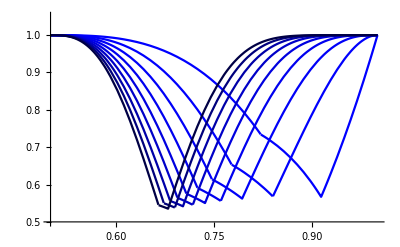

```mathematica
maxprobs[[1,1]]//Simplify
```

```mathematica
prob[2,d,3]
```

2 (1-15 c^2+50 c^3-60 c^4+24 c^5)-1/7 (-1+2 c)^3 (-6 c_0-36 c c_0+66 c^2 c_0-60 c^3 c_0+30 c^4 c_0-c_1-6 c c_1-24 c^2 c_1+60 c^3 c_1-30 c^4 c_1)-2/7 (-1+c)^2 (6 c_0+12 c c_0-87 c^2 c_0+234 c^3 c_0-180 c^4 c_0+120 c^5 c_0+c_1+2 c c_1+3 c^2 c_1-66 c^3 c_1+180 c^4 c_1-120 c^5 c_1)

```mathematica
prob[3,d,3]
```

2 (1-15 c^2+50 c^3-60 c^4+24 c^5)-1/7 (-1+2 c)^3 (-5 c_0-30 c c_0+90 c^2 c_0-120 c^3 c_0+60 c^4 c_0-2 c_1-12 c c_1-48 c^2 c_1+120 c^3 c_1-60 c^4 c_1)-2/7 (-1+c)^2 (5 c_0+10 c c_0-90 c^2 c_0+300 c^3 c_0-360 c^4 c_0+240 c^5 c_0+2 c_1+4 c c_1+6 c^2 c_1-132 c^3 c_1+360 c^4 c_1-240 c^5 c_1)

```mathematica
prob[4,d,3]
```

2 (1-15 c^2+50 c^3-60 c^4+24 c^5)-1/42 (-1+2 c)^3 (-25 c_0-150 c c_0+660 c^2 c_0-1160 c^3 c_0+930 c^4 c_0-420 c^5 c_0+140 c^6 c_0-15 c_1-90 c c_1-360 c^2 c_1+1320 c^3 c_1-1710 c^4 c_1+1260 c^5 c_1-420 c^6 c_1-2 c_2-12 c c_2-48 c^2 c_2-160 c^3 c_2+780 c^4 c_2-840 c^5 c_2+280 c^6 c_2)-1/21 (-1+c)^2 (25 c_0+50 c c_0-555 c^2 c_0+2200 c^3 c_0-3550 c^4 c_0+3300 c^5 c_0-1400 c^6 c_0+560 c^7 c_0+15 c_1+30 c c_1+45 c^2 c_1-1200 c^3 c_1+4170 c^4 c_1-5580 c^5 c_1+4200 c^6 c_1-1680 c^7 c_1+2 c_2+4 c c_2+6 c^2 c_2+8 c^3 c_2-620 c^4 c_2+2280 c^5 c_2-2800 c^6 c_2+1120 c^7 c_2)